```mathematica
(*para={R[θ,ψ]*Sin[θ]*Cos[ψ],R[θ,ψ]*Sin[θ]*Sin[ψ],R[θ,ψ]*Cos[θ]};*)
ϵ=10^-8;
θY=1.0;

(*General equations*)
eq3Dr=(2 R[θ,ψ]^3 Sin[θ]^3-Sin[θ] (Derivative[1,0][R][θ,ψ])^2 (Derivative[0,2][R][θ,ψ]+Cos[θ] Sin[θ] Derivative[1,0][R][θ,ψ])+3 R[θ,ψ] Sin[θ] ((Derivative[0,1][R][θ,ψ])^2+Sin[θ]^2 (Derivative[1,0][R][θ,ψ])^2)+2 Sin[θ] Derivative[0,1][R][θ,ψ] Derivative[1,0][R][θ,ψ] Derivative[1,1][R][θ,ψ]-(Derivative[0,1][R][θ,ψ])^2 (2 Cos[θ] Derivative[1,0][R][θ,ψ]+Sin[θ] Derivative[2,0][R][θ,ψ])-R[θ,ψ]^2 Sin[θ] (Derivative[0,2][R][θ,ψ]+Sin[θ] (Cos[θ] Derivative[1,0][R][θ,ψ]+Sin[θ] Derivative[2,0][R][θ,ψ])))/(R[θ,ψ] (R[θ,ψ]^2 Sin[θ]^2+(Derivative[0,1][R][θ,ψ])^2+Sin[θ]^2 (Derivative[1,0][R][θ,ψ])^2)^(3/2))-(p-R[θ,ψ]*Cos[θ]);

(*Special equations at π*)
EQenπ=-p+2/R[θ,ψ]-R[θ,ψ]-(2 Derivative[2,0][R][θ,ψ])/R[θ,ψ]^2;
(*Special slopem equations at π/2*)
EQslope= Cos[θY] +(Derivative[1,0][R][θ,ψ])/(√(R[θ,ψ]^2+(Derivative[0,1][R][θ,ψ])^2+(Derivative[1,0][R][θ,ψ])^2));



(*standard volume elementary*)
XY=R[θ,ψ]*Sin[θ]*(Cos[θ]R[θ,ψ]+Sin[θ]Derivative[1,0][R][θ,ψ]);
ZZ=R[θ,ψ]*Cos[θ];
dvol=ZZ*XY;
```

```mathematica
(*standard discritisation*)
```

```mathematica
rep={
R[θ,ψ]->Rdis[θi,ψj],
θ->θdis[θi],
ψ->ψdis[ψj],


Derivative[1,0][R][θ,ψ]->(Rdis[θi+1,ψj]-Rdis[θi-1,ψj])/(2*Δθ),
Derivative[0,1][R][θ,ψ]->(Rdis[θi,ψj+1]-Rdis[θi,ψj-1])/(2*Δψ),


Derivative[2,0][R][θ,ψ]->(Rdis[θi+1,ψj]-2*Rdis[θi,ψj]+Rdis[θi-1,ψj])/(Δθ^2),
Derivative[0,2][R][θ,ψ]->(Rdis[θi,ψj+1]-2*Rdis[θi,ψj]+Rdis[θi,ψj-1])/(Δψ^2),

Derivative[1,1][R][θ,ψ]->(Rdis[θi+1,ψj+1]+Rdis[θi-1,ψj-1]-Rdis[θi-1,ψj+1]-Rdis[θi+1,ψj-1])/(4*Δψ*Δθ)
};

(*Replace the boundary cells for equal the number of unkonws and eqs*)
repAngle={
Rdis[θi_,-1]->Rdis[θi,n-1],
Rdis[θi_,n+1]->Rdis[θi,1]
};

repπ={
Rdis[m+1,ψj_]->Rdis[m-1,ψj]
};
```

trouvez le valeur de r

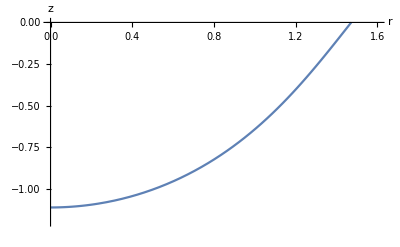

```mathematica
{Vplot,pplot,z0plot,dplot,Lplot}={3.9634264144547195,0.5610521491194301,-1.1124765586221084,1.4715572436681035,1.93493118339818};
(*Print["Vplot:",Vplot,"/pplot:",pplot,"/z0plot:",z0plot,"/dplot:",dplot,"/Lplot:",Lplot]
*)solforme=NDSolve[{
z'[s]==Sin[θ[s]],
r'[s]==Cos[θ[s]],
v'[s]==-2*z[s]*r[s]*Cos[θ[s]],
θ'[s]==pplot-z[s] -  Sin[θ[s]] / r[s],

v[ϵ]==ϵ,
r[ϵ]== ϵ,
θ[ϵ]== ϵ,
z[ϵ]==z0plot},

{z[s],v[s],θ[s],r[s]},{s,ϵ,Lplot}
][[1]];
s0=ParametricPlot[{r[s],z[s]}/.solforme,{s,0,Lplot},
AxesLabel-> {Style["r",FontSize->22],Style["z",FontSize->22]},LabelStyle->{FontSize->22},AspectRatio->1/GoldenRatio,PlotRange->{{0,1.6},{-1.2,0}},AxesStyle->Black]
```

```mathematica
FindRoot[z[s]== -1/.solforme,{s,1}]
```

{s→0.527047}

```mathematica
FindRoot[-z[s]/r[s]==Sin[π/3]/.solforme,{s,1}]
```

{s→0.966928}

equation

```mathematica
(*m is for θ(iθmax),n is for ψ(iψmax)*)
m=14;
n=15;

Δθ=π/(2*m);
Δψ=2*π/n;
```

```mathematica
dvol/.rep
```

Cos[θdis[θi]] Rdis[θi,ψj]^2 Sin[θdis[θi]] (Cos[θdis[θi]] Rdis[θi,ψj]+(7 (-Rdis[-1+θi,ψj]+Rdis[1+θi,ψj]) Sin[θdis[θi]])/π)

```mathematica
(*calculate the values of r based on solution find*)
Rlist={};
Do[
θref=π/2*i/m;
sref=FindRoot[-z[s]/r[s]=={Tan[θref]-0.03}/.solforme,{s,1}];
Rref=Sqrt[(z[s]/.solforme/.sref)^2+(r[s]/.solforme/.sref)^2];
AppendTo[Rlist,Rref];
,{i,0,m-1}];
AppendTo[Rlist,-z[s]/.solforme/.s->0.];
Rneg1=2*Rlist[[1]]-Rlist[[2]];
PrependTo[Rlist,Rneg1];
Rlist
```

InterpolatingFunction::dmval: Input value {1.93606} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.98744} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{1.60039,1.50117,1.40195,1.32802,1.27185,1.22887,1.19601,1.17108,1.15243,1.13872,1.12888,1.12201,1.11742,1.11454,1.11297,1.11248}

```mathematica
(*avoid err caused by number of cells*)
volcorrige=0; 
Do[
Do[
voltest=Δψ*Δθ*dvol/.rep/.{θdis[θi]->(θi*Δθ+π/2)}/.{Rdis[θi,ψj]->Rlist[[θi+2]]}/.{Rdis[θi-1,ψj]->Rlist[[θi+1]]}/.{Rdis[θi+1,ψj]->Rlist[[θi+3]]};
volcorrige=volcorrige+voltest;
,{ψj,0,n-1}];
,{θi,0,m-1}];
volcorrige
```

4.04823

```mathematica
(*test manuel les valeur initial*)
Rlist={1.60,1.4711735708276084,1.3280227401640416,1.2288672396181295,1.1710848596162655,1.138719072439423,1.1220130326719284,1.1145360852504747,1.112476559012462}
```

{1.6,1.47117,1.32802,1.22887,1.17108,1.13872,1.12201,1.11454,1.11248}

```mathematica
listeEQ={};

volumetot=0;

Do[
Do[
(*General rep of equations*)
If[(θi<m),
AppendTo[listeEQ,eq3Dr/.rep/.repAngle/.repπ/.{θdis[θi]->(θi*Δθ+π/2)}]
];

(*special rep of equations at θ=π*)
If[(θi== m),
AppendTo[listeEQ,EQenπ/.rep/.repAngle/.repπ/.{θdis[θi]->(θi*Δθ+π/2)}];
];

If[(θi== 0),
(*Boundary conditions youngs degres*)
AppendTo[listeEQ,EQslope/.rep/.repAngle/.{θdis[θi]->(θi*Δθ+π/2)}];
];

(*Boundary conditions volume*)
If[(θi<m)∧(ψj<n),(* une espece de methode des rectangles pour l integrale de volume *)
dvolhere=Δψ*Δθ*dvol/.rep/.{θdis[θi]->(θi*Δθ+π/2)};
volumetot=volumetot+dvolhere;
];

,{θi,0,m}];
,{ψj,0,n}];

AppendTo[listeEQ,volumetot- Vplot];


(*==(n+1)*(m+2)*)
Length[listeEQ]
listeEQ;
```

257

```mathematica
(*initial values*)
initialVALUE={};
Do[
Do[
AppendTo[initialVALUE,{Rdis[i,j],Rlist[[i+2]]+0.02}];
,{j,0,n}];
,{i,-1,m}];

AppendTo[initialVALUE,{p,pplot}];
Length[initialVALUE]
initialVALUE;
```

257

```mathematica
(*Solve values*)
fr3Dns=FindRoot[listeEQ,initialVALUE,{Jacobian->{"FiniteDifference"}}]
```

{Rdis[-1,0]→1.58707,Rdis[-1,1]→1.58707,Rdis[-1,2]→1.58707,Rdis[-1,3]→1.58707,Rdis[-1,4]→1.58707,Rdis[-1,5]→1.58707,Rdis[-1,6]→1.58707,Rdis[-1,7]→1.58707,Rdis[-1,8]→1.58707,Rdis[-1,9]→1.58707,Rdis[-1,10]→1.58707,Rdis[-1,11]→1.58707,Rdis[-1,12]→1.58707,Rdis[-1,13]→1.58707,Rdis[-1,14]→1.58707,Rdis[-1,15]→1.58707,Rdis[0,0]→1.4645,Rdis[0,1]→1.4645,Rdis[0,2]→1.4645,Rdis[0,3]→1.4645,Rdis[0,4]→1.4645,Rdis[0,5]→1.4645,Rdis[0,6]→1.4645,Rdis[0,7]→1.4645,Rdis[0,8]→1.4645,Rdis[0,9]→1.4645,Rdis[0,10]→1.4645,Rdis[0,11]→1.4645,Rdis[0,12]→1.4645,Rdis[0,13]→1.4645,Rdis[0,14]→1.4645,Rdis[0,15]→1.4645,Rdis[1,0]→1.37606,Rdis[1,1]→1.37606,Rdis[1,2]→1.37606,Rdis[1,3]→1.37606,Rdis[1,4]→1.37606,Rdis[1,5]→1.37606,Rdis[1,6]→1.37606,Rdis[1,7]→1.37606,Rdis[1,8]→1.37606,Rdis[1,9]→1.37606,Rdis[1,10]→1.37606,Rdis[1,11]→1.37606,Rdis[1,12]→1.37606,Rdis[1,13]→1.37606,Rdis[1,14]→1.37606,Rdis[1,15]→1.37606,Rdis[2,0]→1.31012,Rdis[2,1]→1.31012,Rdis[2,2]→1.31012,Rdis[2,3]→1.31012,Rdis[2,4]→1.31012,Rdis[2,5]→1.31012,Rdis[2,6]→1.31012,Rdis[2,7]→1.31012,Rdis[2,8]→1.31012,Rdis[2,9]→1.31012,Rdis[2,10]→1.31012,Rdis[2,11]→1.31012,Rdis[2,12]→1.31012,Rdis[2,13]→1.31012,Rdis[2,14]→1.31012,Rdis[2,15]→1.31012,Rdis[3,0]→1.2602,Rdis[3,1]→1.2602,Rdis[3,2]→1.2602,Rdis[3,3]→1.2602,Rdis[3,4]→1.2602,Rdis[3,5]→1.2602,Rdis[3,6]→1.2602,Rdis[3,7]→1.2602,Rdis[3,8]→1.2602,Rdis[3,9]→1.2602,Rdis[3,10]→1.2602,Rdis[3,11]→1.2602,Rdis[3,12]→1.2602,Rdis[3,13]→1.2602,Rdis[3,14]→1.2602,Rdis[3,15]→1.2602,Rdis[4,0]→1.22221,Rdis[4,1]→1.22221,Rdis[4,2]→1.22221,Rdis[4,3]→1.22221,Rdis[4,4]→1.22221,Rdis[4,5]→1.22221,Rdis[4,6]→1.22221,Rdis[4,7]→1.22221,Rdis[4,8]→1.22221,Rdis[4,9]→1.22221,Rdis[4,10]→1.22221,Rdis[4,11]→1.22221,Rdis[4,12]→1.22221,Rdis[4,13]→1.22221,Rdis[4,14]→1.22221,Rdis[4,15]→1.22221,Rdis[5,0]→1.19339,Rdis[5,1]→1.19339,Rdis[5,2]→1.19339,Rdis[5,3]→1.19339,Rdis[5,4]→1.19339,Rdis[5,5]→1.19339,Rdis[5,6]→1.19339,Rdis[5,7]→1.19339,Rdis[5,8]→1.19339,Rdis[5,9]→1.19339,Rdis[5,10]→1.19339,Rdis[5,11]→1.19339,Rdis[5,12]→1.19339,Rdis[5,13]→1.19339,Rdis[5,14]→1.19339,Rdis[5,15]→1.19339,Rdis[6,0]→1.17173,Rdis[6,1]→1.17173,Rdis[6,2]→1.17173,Rdis[6,3]→1.17173,Rdis[6,4]→1.17173,Rdis[6,5]→1.17173,Rdis[6,6]→1.17173,Rdis[6,7]→1.17173,Rdis[6,8]→1.17173,Rdis[6,9]→1.17173,Rdis[6,10]→1.17173,Rdis[6,11]→1.17173,Rdis[6,12]→1.17173,Rdis[6,13]→1.17173,Rdis[6,14]→1.17173,Rdis[6,15]→1.17173,Rdis[7,0]→1.15569,Rdis[7,1]→1.15569,Rdis[7,2]→1.15569,Rdis[7,3]→1.15569,Rdis[7,4]→1.15569,Rdis[7,5]→1.15569,Rdis[7,6]→1.15569,Rdis[7,7]→1.15569,Rdis[7,8]→1.15569,Rdis[7,9]→1.15569,Rdis[7,10]→1.15569,Rdis[7,11]→1.15569,Rdis[7,12]→1.15569,Rdis[7,13]→1.15569,Rdis[7,14]→1.15569,Rdis[7,15]→1.15569,Rdis[8,0]→1.14407,Rdis[8,1]→1.14407,Rdis[8,2]→1.14407,Rdis[8,3]→1.14407,Rdis[8,4]→1.14407,Rdis[8,5]→1.14407,Rdis[8,6]→1.14407,Rdis[8,7]→1.14407,Rdis[8,8]→1.14407,Rdis[8,9]→1.14407,Rdis[8,10]→1.14407,Rdis[8,11]→1.14407,Rdis[8,12]→1.14407,Rdis[8,13]→1.14407,Rdis[8,14]→1.14407,Rdis[8,15]→1.14407,Rdis[9,0]→1.13586,Rdis[9,1]→1.13586,Rdis[9,2]→1.13586,Rdis[9,3]→1.13586,Rdis[9,4]→1.13586,Rdis[9,5]→1.13586,Rdis[9,6]→1.13586,Rdis[9,7]→1.13586,Rdis[9,8]→1.13586,Rdis[9,9]→1.13586,Rdis[9,10]→1.13586,Rdis[9,11]→1.13586,Rdis[9,12]→1.13586,Rdis[9,13]→1.13586,Rdis[9,14]→1.13586,Rdis[9,15]→1.13586,Rdis[10,0]→1.13026,Rdis[10,1]→1.13026,Rdis[10,2]→1.13026,Rdis[10,3]→1.13026,Rdis[10,4]→1.13026,Rdis[10,5]→1.13026,Rdis[10,6]→1.13026,Rdis[10,7]→1.13026,Rdis[10,8]→1.13026,Rdis[10,9]→1.13026,Rdis[10,10]→1.13026,Rdis[10,11]→1.13026,Rdis[10,12]→1.13026,Rdis[10,13]→1.13026,Rdis[10,14]→1.13026,Rdis[10,15]→1.13026,Rdis[11,0]→1.12659,Rdis[11,1]→1.12659,Rdis[11,2]→1.12659,Rdis[11,3]→1.12659,Rdis[11,4]→1.12659,Rdis[11,5]→1.12659,Rdis[11,6]→1.12659,Rdis[11,7]→1.12659,Rdis[11,8]→1.12659,Rdis[11,9]→1.12659,Rdis[11,10]→1.12659,Rdis[11,11]→1.12659,Rdis[11,12]→1.12659,Rdis[11,13]→1.12659,Rdis[11,14]→1.12659,Rdis[11,15]→1.12659,Rdis[12,0]→1.12435,Rdis[12,1]→1.12435,Rdis[12,2]→1.12435,Rdis[12,3]→1.12435,Rdis[12,4]→1.12435,Rdis[12,5]→1.12435,Rdis[12,6]→1.12435,Rdis[12,7]→1.12435,Rdis[12,8]→1.12435,Rdis[12,9]→1.12435,Rdis[12,10]→1.12435,Rdis[12,11]→1.12435,Rdis[12,12]→1.12435,Rdis[12,13]→1.12435,Rdis[12,14]→1.12435,Rdis[12,15]→1.12435,Rdis[13,0]→1.12315,Rdis[13,1]→1.12315,Rdis[13,2]→1.12315,Rdis[13,3]→1.12315,Rdis[13,4]→1.12315,Rdis[13,5]→1.12315,Rdis[13,6]→1.12315,Rdis[13,7]→1.12315,Rdis[13,8]→1.12315,Rdis[13,9]→1.12315,Rdis[13,10]→1.12315,Rdis[13,11]→1.12315,Rdis[13,12]→1.12315,Rdis[13,13]→1.12315,Rdis[13,14]→1.12315,Rdis[13,15]→1.12315,Rdis[14,0]→1.12277,Rdis[14,1]→1.12277,Rdis[14,2]→1.12277,Rdis[14,3]→1.12277,Rdis[14,4]→1.12277,Rdis[14,5]→1.12277,Rdis[14,6]→1.12277,Rdis[14,7]→1.12277,Rdis[14,8]→1.12277,Rdis[14,9]→1.12277,Rdis[14,10]→1.12277,Rdis[14,11]→1.12277,Rdis[14,12]→1.12277,Rdis[14,13]→1.12277,Rdis[14,14]→1.12277,Rdis[14,15]→1.12277,p→0.5637}

```mathematica
initialVALUE
```

{{Rdis[-1,0],1.69432},{Rdis[-1,1],1.69432},{Rdis[-1,2],1.69432},{Rdis[-1,3],1.69432},{Rdis[-1,4],1.69432},{Rdis[-1,5],1.69432},{Rdis[0,0],1.52117},{Rdis[0,1],1.52117},{Rdis[0,2],1.52117},{Rdis[0,3],1.52117},{Rdis[0,4],1.52117},{Rdis[0,5],1.52117},{Rdis[1,0],1.34802},{Rdis[1,1],1.34802},{Rdis[1,2],1.34802},{Rdis[1,3],1.34802},{Rdis[1,4],1.34802},{Rdis[1,5],1.34802},{Rdis[2,0],1.24887},{Rdis[2,1],1.24887},{Rdis[2,2],1.24887},{Rdis[2,3],1.24887},{Rdis[2,4],1.24887},{Rdis[2,5],1.24887},{Rdis[3,0],1.19108},{Rdis[3,1],1.19108},{Rdis[3,2],1.19108},{Rdis[3,3],1.19108},{Rdis[3,4],1.19108},{Rdis[3,5],1.19108},{Rdis[4,0],1.15872},{Rdis[4,1],1.15872},{Rdis[4,2],1.15872},{Rdis[4,3],1.15872},{Rdis[4,4],1.15872},{Rdis[4,5],1.15872},{Rdis[5,0],1.14201},{Rdis[5,1],1.14201},{Rdis[5,2],1.14201},{Rdis[5,3],1.14201},{Rdis[5,4],1.14201},{Rdis[5,5],1.14201},{Rdis[6,0],1.13454},{Rdis[6,1],1.13454},{Rdis[6,2],1.13454},{Rdis[6,3],1.13454},{Rdis[6,4],1.13454},{Rdis[6,5],1.13454},{Rdis[7,0],1.13248},{Rdis[7,1],1.13248},{Rdis[7,2],1.13248},{Rdis[7,3],1.13248},{Rdis[7,4],1.13248},{Rdis[7,5],1.13248},{p,0.561052}}

```mathematica
listeEQ/.fr3Dns
```

{-5.55112×10^-16,2.22045×10^-16,0.,-1.77636×10^-15,1.33227×10^-15,3.10862×10^-15,1.9984×10^-15,1.39888×10^-14,1.26565×10^-14,-1.11022×10^-15,1.11022×10^-16,-2.22045×10^-16,1.55431×10^-15,-1.33227×10^-15,1.11022×10^-15,6.21725×10^-15,1.24345×10^-14,1.42109×10^-14,-2.22045×10^-16,3.33067×10^-16,-2.22045×10^-16,-1.11022×10^-15,1.9984×10^-15,3.55271×10^-15,4.66294×10^-15,3.55271×10^-15,2.69784×10^-14,-1.33227×10^-15,1.11022×10^-16,3.33067×10^-16,1.11022×10^-15,-2.22045×10^-15,2.88658×10^-15,7.99361×10^-15,8.21565×10^-15,1.19904×10^-14,-1.9984×10^-15,2.22045×10^-16,0.,8.88178×10^-16,0.,2.44249×10^-15,3.55271×10^-15,7.54952×10^-15,2.40918×10^-14,-3.33067×10^-16,1.11022×10^-16,-2.22045×10^-15,1.33227×10^-15,1.33227×10^-15,2.22045×10^-16,8.65974×10^-15,3.55271×10^-15,1.31006×10^-14,-1.33227×10^-15}

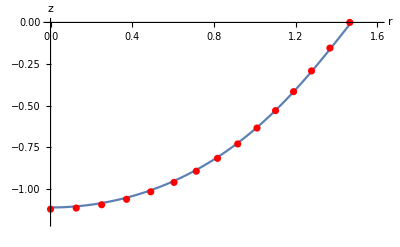

{{1.4645,0.},{1.36741,-0.15407},{1.27728,-0.29153},{1.18948,-0.416217},{1.10117,-0.530296},{1.01047,-0.63492},{0.916093,-0.73056},{0.817199,-0.817199},{0.713316,-0.894469},{0.604315,-0.961762},{0.4904,-1.01833},{0.372089,-1.06337},{0.250191,-1.09616},{0.125753,-1.11609},{0.,-1.12277}}

```mathematica
(*Compare plot*)
newplot={};
newplot2={};
Do[
xplot= (Rdis[i,0]/.fr3Dns) *Cos[π/2*(i/m)];
yplot=-(Rdis[i,0]/.fr3Dns) *Sin[π/2*(i/m)];

xxplot= Rlist[[i+2]]*Cos[π/2*(i/m)];
yyplot=-Rlist[[i+2]]*Sin[π/2*(i/m)];


AppendTo[newplot, {xplot,yplot}];
AppendTo[newplot2, {xxplot,yyplot}];
,{i,0,m}];
s1=ListPlot[newplot,PlotStyle->{Red}];
s2=ListPlot[newplot2,PlotStyle->{Green}];
Show[s0,s1,AxesLabel-> {Style["r",FontSize->22],Style["z",FontSize->22]},LabelStyle->{FontSize->22},AxesStyle->Black]
Print[newplot]
```

```mathematica
volveri=0;
Δθ=π/(2*m);
Δψ=2*π/n;
Do[
Do[
voltest=Δψ*Δθ*dvol/.rep/.fr3Dns/.{θdis[θi]->(θi*Δθ+π/2)};
volveri=volveri+voltest;
,{ψj,0,n-1}];
,{θi,0,m-1}];
volveri
Vplot
```

3.96343

3.96343